```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/oernst/Research/cnl/dynamic_boltzmann_cpp

Params

```mathematica
nOpt=200;
```

```mathematica
numin=-2.5;
numax=-1.0;
nnu=41;
dnu=(numax-numin)/(nnu-1);
nuGrid=Table[numin+i*dnu,{i,0,nnu-1}];
```

In depth

```mathematica
Manipulate[
f=Import["data/F/"<>IntegerString[iOptStep,10,4]<>".txt","Table"];
nu=Import["data/nu_traj/"<>IntegerString[iOptStep,10,4]<>".txt","Table"];
var=Import["data/var_traj/"<>IntegerString[iOptStep,10,4]<>".txt","Table"];
moments=Import["data/moments/"<>IntegerString[iOptStep,10,4]<>".txt","Table"];
tvals=nu[[;;,1]];
nuTraj=nu[[;;,2]];
varSel=var[[inuVal;;,3]][[;;;;nnu]];
pltave=ListLinePlot[{moments[[;;,2]],moments[[;;,3]]}];
pltvar=ListLinePlot[{varSel,varSel*Table[Exp[-(nuTraj[[it]]-nuGrid[[inuVal]])^2/(2*0.004)],{it,1,Length[nu]}]},PlotLabel->nuGrid[[inuVal]]];
pltf=Show[{
ListLinePlot[f,PlotRange->All,PlotStyle->Black]
,
Plot[Exp[x]-1,{x,-2.5,-1}]
},PlotRange->All];

GraphicsGrid[{{pltf,},{pltave,pltvar}}]
,{iOptStep,0,nOpt-1,1},{{inuVal,25},1,Length[nuGrid],1}]
```

```mathematica
cum={};
AppendTo[cum,(moments[[1,2]]-moments[[1,3]])*interp[tvals[[1]],nuVal]];
Do[
AppendTo[cum,cum[[-1]]+(moments[[t,2]]-moments[[t,3]])*interp[tvals[[t]],nuVal]];
,{t,2,Length[tvals]}]
```

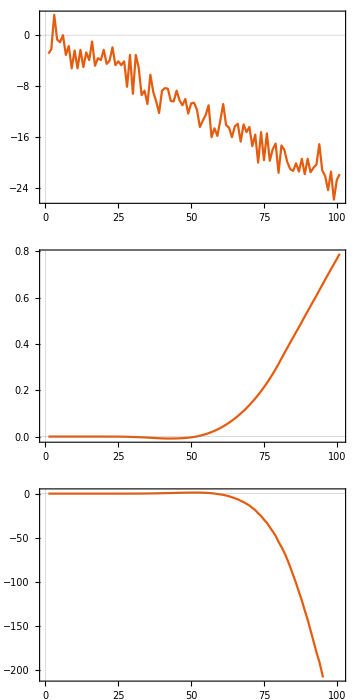

```mathematica
GraphicsColumn[{
ListLinePlot[moments[[;;,2]]-moments[[;;,3]]],
ListLinePlot[Table[interp[tvals[[t]],nuVal],{t,1,Length[tvals]}]],
ListLinePlot[cum]
},ImageSize->Medium]
```

Moments

```mathematica
Manipulate[
moments=Import["data/moments/"<>IntegerString[i,10,4]<>".txt","Table"];
GraphicsColumn[{
Show[
ListLinePlot[moments[[;;,{1,2}]],PlotRange->All,PlotStyle->Black]
,
ListLinePlot[moments[[;;,{1,3}]],PlotRange->All,PlotStyle->Black]
]
}]
,
{i,0,nOpt-1,1}]
```

Variational term

```mathematica
Manipulate[
nu=Import["data/nu_traj/"<>IntegerString[i,10,4]<>".txt","Table"];
var=Import["data/var_traj/"<>IntegerString[i,10,4]<>".txt","Table"];
GraphicsColumn[{
Show[
ListContourPlot[var]
,
ListLinePlot[nu,PlotRange->All,PlotStyle->Black]
]
}]
,
{i,0,nOpt-1,1}]
```

Basis function

```mathematica
z=Sum[Exp[n*v[t]],{n,0,Infinity}]
```

-1/(-1+ⅇ^v[t])

```mathematica
ave=Sum[n*Exp[n*v[t]]/z,{n,0,Infinity}]
```

-ⅇ^v[t]/(-1+ⅇ^v[t])

```mathematica
Solve[(D[ave,t]==-ave)/.v'[t]->dv,dv]
```

{{dv→-1+ⅇ^v[t]}}

```mathematica
Manipulate[
f=Import["data/F/"<>IntegerString[i,10,4]<>".txt","Table"];
Show[{
ListLinePlot[f,PlotRange->All,PlotStyle->Black]
,
Plot[Exp[x]-1,{x,-3,-1}]
},PlotRange->All]
,
{i,0,nOpt-1,1}]
```